# Invariance

## Environment

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],CellContext->Notebook];
Off[Solve::ifun];
```

## Boxes

```mathematica
MakeBoxes[a3,StandardForm]:=SubscriptBox["a","3"];
MakeExpression[SubscriptBox["a","3"],StandardForm]:=MakeExpression["a3",StandardForm];
MakeBoxes[c3,StandardForm]:=SubscriptBox["c","3"];
MakeExpression[SubscriptBox["c","3"],StandardForm]:=MakeExpression["c3",StandardForm];
MakeBoxes[dtB,StandardForm]:=SuperscriptBox["dt","B"];
MakeExpression[SuperscriptBox["dt","B"],StandardForm]:=MakeExpression["dtB",StandardForm];
MakeBoxes[dtG,StandardForm]:=SuperscriptBox["dt","G"];
MakeExpression[SuperscriptBox["dt","G"],StandardForm]:=MakeExpression["dtG",StandardForm];
MakeBoxes[dtR,StandardForm]:=SuperscriptBox["dt","R"];
MakeExpression[SuperscriptBox["dt","R"],StandardForm]:=MakeExpression["dtR",StandardForm];
MakeBoxes[ds2,StandardForm]:=SuperscriptBox["ds","2"];
MakeExpression[SuperscriptBox["ds","2"],StandardForm]:=MakeExpression["ds2",StandardForm];
MakeBoxes[dxC,StandardForm]:=SuperscriptBox["dx","C"];
MakeExpression[SuperscriptBox["dx","C"],StandardForm]:=MakeExpression["dxC",StandardForm];
MakeBoxes[dxM,StandardForm]:=SuperscriptBox["dx","M"];
MakeExpression[SuperscriptBox["dx","M"],StandardForm]:=MakeExpression["dxM",StandardForm];
MakeBoxes[dxtM,StandardForm]:=SubsuperscriptBox["dx","t","M"];
MakeExpression[SubsuperscriptBox["dx","t","M"],StandardForm]:=MakeExpression["dxtM",StandardForm];
MakeBoxes[dxtY,StandardForm]:=SubsuperscriptBox["dx","t","Y"];
MakeExpression[SubsuperscriptBox["dx","t","Y"],StandardForm]:=MakeExpression["dxtY",StandardForm];
MakeBoxes[dxY,StandardForm]:=SuperscriptBox["dx","Y"];
MakeExpression[SuperscriptBox["dx","Y"],StandardForm]:=MakeExpression["dxY",StandardForm];
MakeBoxes[dxyM,StandardForm]:=SubsuperscriptBox["dx","y","M"];
MakeExpression[SubsuperscriptBox["dx","y","M"],StandardForm]:=MakeExpression["dxyM",StandardForm];
MakeBoxes[dxyY,StandardForm]:=SubsuperscriptBox["dx","y","Y"];
MakeExpression[SubsuperscriptBox["dx","y","Y"],StandardForm]:=MakeExpression["dxyY",StandardForm];
MakeBoxes[dyM,StandardForm]:=SuperscriptBox["dy","M"];
MakeExpression[SuperscriptBox["dy","M"],StandardForm]:=MakeExpression["dyM",StandardForm];MakeBoxes[dyY,StandardForm]:=SuperscriptBox["dy","Y"];
MakeExpression[SuperscriptBox["dy","Y"],StandardForm]:=MakeExpression["dyY",StandardForm];
MakeBoxes[properSpace,StandardForm]:=SuperscriptBox["x","′"];
MakeExpression[SuperscriptBox["x","′"],StandardForm]:=MakeExpression["properSpace",StandardForm];
MakeBoxes[properTime,StandardForm]:=SuperscriptBox["t","′"];
MakeExpression[SuperscriptBox["t","′"],StandardForm]:=MakeExpression["properTime",StandardForm];MakeBoxes[t0,StandardForm]:=SubscriptBox["t","0"];
MakeExpression[SubscriptBox["t","0"],StandardForm]:=MakeExpression["t0",StandardForm];
MakeBoxes[tB,StandardForm]:=SuperscriptBox["t","B"];
MakeExpression[SuperscriptBox["t","B"],StandardForm]:=MakeExpression["tB",StandardForm];
MakeBoxes[tG,StandardForm]:=SuperscriptBox["t","G"];
MakeExpression[SuperscriptBox["t","G"],StandardForm]:=MakeExpression["tG",StandardForm];
MakeBoxes[tR,StandardForm]:=SuperscriptBox["t","R"];
MakeExpression[SuperscriptBox["t","R"],StandardForm]:=MakeExpression["tR",StandardForm];
MakeBoxes[xM,StandardForm]:=SuperscriptBox["x","M"];
MakeExpression[SuperscriptBox["x","M"],StandardForm]:=MakeExpression["xM",StandardForm];MakeBoxes[xY,StandardForm]:=SuperscriptBox["x","Y"];
MakeExpression[SuperscriptBox["x","Y"],StandardForm]:=MakeExpression["xY",StandardForm];MakeBoxes[yM,StandardForm]:=SuperscriptBox["y","M"];
MakeExpression[SuperscriptBox["y","M"],StandardForm]:=MakeExpression["yM",StandardForm];
MakeBoxes[θM,StandardForm]:=SuperscriptBox["θ","M"];
MakeExpression[SuperscriptBox["θ","M"],StandardForm]:=MakeExpression["θM",StandardForm];MakeBoxes[θY,StandardForm]:=SuperscriptBox["θ","Y"];
MakeExpression[SuperscriptBox["θ","Y"],StandardForm]:=MakeExpression["θY",StandardForm];
```

## Units

```mathematica
s=1;
m=1;
cm=0.01 m;
kg=1;
g=0.001 kg;
J=(kg m^2)/s^2;
K=1;
km=1000 m;
yr=60 60 24 365.25 s;
kyr=1000 yr;
Myr=1000 kyr;
Gyr=1000 Myr;
pc=3.08567758 10^13 km;
kpc=1000 pc;
Mpc=1000 kpc;
Gpc=1000 Mpc;
```

## Constants

```mathematica
G=6.67408 10^-11 m^3/(kg s^2);
ℏ=6.62607004 10^-34 J s;
Subscript[c, 3]=2.99792458 10^8 m/s;
Subscript[k, B]=1.380649 10^-23 J/K;
Subscript[a, B]=(8 π^5 Subscript[k, B]^4)/(15 ℏ^3 Subscript[c, 3]^3)J/(m^3 K^4);
Subscript[a, 3]=4.38693 10^-11 m/s^2;
Subscript[t, 0]=8.57697 10^17 s;
Subscript[η, 0]=Subscript[η, t][Subscript[t, 0]];
h=2/(100 Subscript[t, 0])Mpc/km;
Subscript[H, 0]=h 100 km/(s Mpc);
Subscript[T, 0]=2.7255 K;
θ100=1.0411;
Subscript[A, He]=0.25;
Subscript[A, H]=0.75;
Subscript[m, He]=6.6464764 10^-27 kg;
Subscript[m, H]=1.6735575 10^-27 kg;
Subscript[σ, T]=6.6524 10^-29 m^2;
Subscript[ρ, γ]=(Subscript[a, B] Subscript[T, 0]^4)/Subscript[c, 3]^2 kg/m^3;
```

## Clear Variables

```mathematica
ClearAll[dt^R,Subscript[dx, y]^Y,Subscript[dx, t]^Y,ds^2,Subscript[dx, t]^M,dt^B,Subscript[dx, y]^M,θ,dx^M,dx^Y,Subscript[a, 3],Subscript[c, 3],t,c,γ,t',t^B,x',x^M]
```

## QES Invariance

### Distance of one second in the Inertial Frame (dx^Y = 0).

Calculate the length of one second in the observer’s frame knowing that the observer doesn’t move.  Note that we’re using the Green-Red plane as the reference frame. Red-Blue plane is the frame of the moving object.

```mathematica
dt^R=1;
Subscript[dx, y]^Y=0;
```

```mathematica
Subscript[dx, t]^Y=Subscript[dx, t]^Y/.Solve[Subscript[dx, t]^Y/(ⅈ dt^R)==∫Subscript[a, 3] ⅆ t^R+Subscript[c, 3],Subscript[dx, t]^Y]⟦1⟧;
```

```mathematica
ds^2=ds^2/.Simplify[Solve[ds^2==(Subscript[dx, t]^Y/(ⅈ dt^R))^2(ⅈ dt^R)^2+(Subscript[dx, y]^Y/dy^Y)^2(dy^Y)^2,ds^2]]⟦1⟧
```

-(c_3+a_3 t^R)^2

### Proper Space as a function of angle.

```mathematica
Subscript[dx, t]^M=Subscript[dx, t]^M/.Solve[Subscript[dx, t]^M/(ⅈ dt^B)==∫Subscript[a, 3] ⅆ t^B+Subscript[c, 3],Subscript[dx, t]^M][[1]]
dt^B=dt^B/.Simplify[Solve[dt^R/dt^B==Cos[θ],dt^B]]⟦1⟧
```

ⅈ dt^B (c_3+a_3 t^B)

Sec[θ]

```mathematica
ds^2==(Subscript[dx, t]^M/(ⅈ dt^B))^2 (ⅈ dt^B)^2+(Subscript[dx, y]^M/dy^M)^2 (dy^M)^2
```

-(c_3+a_3 t^R)^2==(dx_y^M)^2-(c_3+a_3 t^B)^2 Sec[θ]^2

```mathematica
Simplify[ds^2==(Subscript[dx, t]^M/(ⅈ dt^B))^2 (ⅈ dt^B)^2+(Subscript[dx, y]^M/dy^M)^2 (dy^M)^2]
```

(c_3+a_3 t^B)^2 Sec[θ]^2==(dx_y^M)^2+(c_3+a_3 t^R)^2

```mathematica
Subscript[dx, y]^M=Subscript[dx, y]^M/.Simplify[Solve[ds^2==(Subscript[dx, t]^M/(ⅈ dt^B))^2 (ⅈ dt^B)^2+(Subscript[dx, y]^M/dy^M)^2 (dy^M)^2,Subscript[dx, y]^M]/.{t^R->t,t^B->t}]⟦1⟧
```

-√((c_3+a_3 t)^2 Tan[θ]^2)

### Angle as a function of spatial velocity.

```mathematica
θ=θ/.Simplify[Solve[Subscript[dx, y]^M/(ⅈ dt^B)==ⅈ v,θ]][[1]]
```

ArcSin[v/(c_3+a_3 t)]

### Coordinate time vs. Proper Time

```mathematica
dt^R/dt^B
```

√(1-v^2/(c_3+a_3 t)^2)

### Proper Space vs Coordinate Space

```mathematica
dx^M=ⅈ^2 ϕ t^R t^B Cos[θ^M];
dx^Y=ⅈ^2 ϕ t^R t^G Cos[θ^Y];
dx^M/dx^Y/.{θ^Y->0,t^G->t^B,θ^M->θ}
```

√(1-v^2/(c_3+a_3 t)^2)

### Proper Time and Space vs . Velocity

```mathematica
Subscript[a, 3]=4.38693 10^-11 m/s^2;
Subscript[c, 3]=2.99792458 10^8 m/s;
t=8.57697 10^17 s;
```

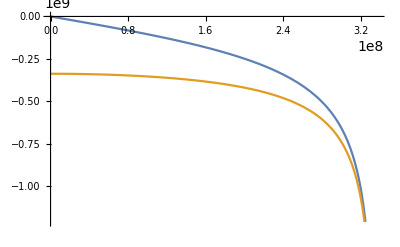

```mathematica
Plot[{Subscript[dx, y]^M ,ⅈ dt^B ⅈ(Subscript[c, 3]+Subscript[a, 3] t)},{v,0,Subscript[c, 3]+Subscript[a, 3] t}]
```

### Proper Velocity

Just a checksum on the formulas for proper space and proper time.  This should be a linear plot .

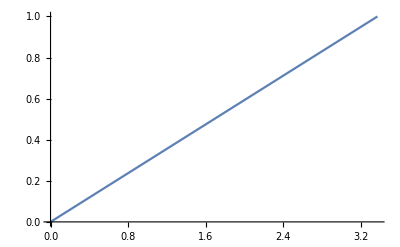

```mathematica
Plot[{Subscript[dx, y]^M/(ⅈ dt^B ⅈ(Subscript[c, 3]+Subscript[a, 3] t))},{v,0,Subscript[c, 3]+Subscript[a, 3] t}]
```

## QES vs. Lorentz Invariance

```mathematica
ClearAll[Subscript[a, 3],Subscript[c, 3],t]
```

```mathematica
c=1;
```

### Lorentz Factor

```mathematica
γ[v_]:=1/(√(1-v^2/c^2))
```

### Lorentz Proper Time

```mathematica
t'=γ[v] (t-(v x)/c^2)/.{t->1,x->1}
```

(1-v)/(√(1-v^2))

```mathematica
t^B=t^B/.Solve[(ⅈ dt^R)/(ⅈ dt^B)==t^B,t^B][[1]]/.Subscript[c, 3]+Subscript[a, 3] t->1
```

√(1-v^2)

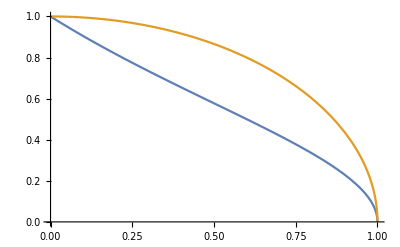

```mathematica
Plot[{t',t^B},{v,0,1}]
```

### Lorentz Proper Space

```mathematica
x'=γ[v](x-v t)/.{t->1,x->1}
```

(1-v)/(√(1-v^2))

```mathematica
x^M=dx^M/dx^Y/.{θ^Y->0,t^G->t^B,θ^M->θ}/.Subscript[c, 3]+Subscript[a, 3] t->1
```

√(1-v^2)

```mathematica
Plot[{x',x^M},{v,0,1}]
```

-Graphics-